```mathematica
解微分方程
建立方程
```

```mathematica
eqn={(500+20*t)*p'[t]==420*E^(-(2*t)/25)-40*p[t],p[0]==10.5}
```

{(500+20 t) p'[t]==420 ⅇ^(-2 t/25)-40 p[t],p[0]==10.5}

```mathematica
求解对应规则
```

```mathematica
sol=DSolve[eqn,{p[t]},{t}]
```

{{p[t]→-(262.5 ⅇ^(-2 t/25) (37.5-62.5 ⅇ^(2 t/25)+t))/(25.+t)^2}}

```mathematica
画图
```

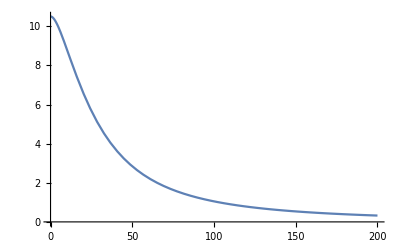

```mathematica
Plot[p[t]/.sol,{t,0,200}]
```